```mathematica
RiePrimeCnt[n_]:=Sum[PrimePi[n^(1/j)]/j,{j,1,Log[2,n]}]
LinnikApprox[n_]:=Sum[(-1)^(j+1)/j (-1)^j (1-n Sum[(-Log[n])^k/k!,{k,0,j–1}]),{j,1,Infinity}]
Table[{N[LinnikApprox[10^n]],N[LogIntegral[10^n]-Log[Log[10^n]]-EulerGamma]},{n,1,4}]//TableForm
```

$Aborted

```mathematica
LogIntegral[ 100.]-Log[Log[100.]]-EulerGamma
```

28.0217

```mathematica
-Gamma[ 0,  -Log[100.]]-Pi I-Log[Log[100]] -EulerGamma
```

28.0217+0. ⅈ

```mathematica
TestSum[n_,z_,t_,s_]:=1+Sum[N[Binomial[z,k] (-1)^k (Gamma[k,0,(s-1)Log[n]]/(Gamma[k](1-s)^k))],{k,1,t}]
ff[ n_, z_, t_,s_] := (Sum[ Binomial[z,k] (-1)^k (  1-Gamma[ k, (s-1)Log[n]]/(Gamma[k](1-s)^k)),{k,0, t}]-1)/z
ff2[ n_, z_, t_,s_] := 1+Sum[ Binomial[z,k] (-1)^k ( Gamma[ k, 0, (s-1)Log[n]]/(Gamma[k](1-s)^k)),{k,1, t}]
```

```mathematica
N[Limit[ ff[ 120, z, 30,-1], z->0]]
```

1675.72+3.76482×10^-24 ⅈ

```mathematica
1-Log[1000.]
```

-5.90776

```mathematica
N[Gamma[2, -Log[200]]]/200
```

-4.29832+5.26392×10^-16 ⅈ

```mathematica
ff2[120.,3,2000,0]
```

2644.2-3.92488×10^-13 ⅈ

```mathematica
N[Gamma[3, -Log[100]]]
```

1399.73-3.42834×10^-13 ⅈ

Integrate::idiv: Integral of ⅇ^-t/t does not converge on {-Log[100], 0}.

```mathematica
ff4[ n_, z_,tt_,s_] := 1+Sum[Integrate[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^((s-1)t),{t,-Log[n],0}],{k,0, tt}]
```

```mathematica
ff2[120.,3,1000,2]
N[ff4[ 120,3,30,2]]
```

7.68658

7.68658

```mathematica
ff5[ n_, z_, s_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^((s-1)t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
Limit[ (ff5[ n, z,s])/z,z->0]
```

Limit[(∫_(-Log[n])^0 ⅇ^((-1+s) t) z Hypergeometric1F1[1-z,2,t]ⅆt)/z,z→0]

```mathematica
Log[10.]
```

2.30259

```mathematica
-1.+LaguerreL[-1. z,Log[10]]/.z->2
```

32.0259

```mathematica
N[Limit[ (LaguerreL[-z,Log[100]]-1)/z,z->0]]
```

28.0217

```mathematica
-1.+LaguerreL[-1,Log[10]]
```

9.

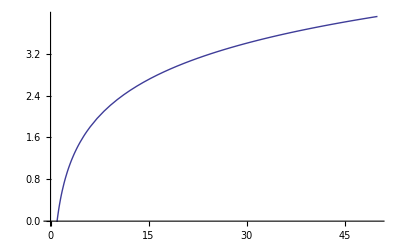

```mathematica
Plot[ Re[-1+LaguerreL[1, -Log[n]]],{n,0,50}]
```

```mathematica
N[ff2[ 1000, -2+I, 1000]]
```

27.1002+19.121 ⅈ

```mathematica
N[LaguerreL[ 2+I, Log[1000]]]
```

27.1002-19.121 ⅈ

```mathematica
N[Limit[ (LaguerreL[-z, Log[20]]-1)/z, z->0]]
```

8.2309

```mathematica
LogIntegral[ 20.]-Log[Log[20.]]-EulerGamma
```

8.2309

```mathematica
ExpIntegralEi[ZetaZero[1]Log[1000.]]
```

-0.0879017+3.45317 ⅈ

```mathematica
Limit[ N[(LaguerreL[ -z, ZetaZero[1]Log[1000]]-1)/z],z->0]+Log[ZetaZero[1] Log[1000]]+EulerGamma
```

-0.0879017+3.45317 ⅈ

```mathematica
N[E^EulerGamma]
```

1.78107

```mathematica
N[Limit[( LaguerreL[-z,Log[100]]-1)/z,z->0]]
```

28.0217

```mathematica
N[LogIntegral[100]-Log[Log[100]]-EulerGamma]
```

28.0217

```mathematica
Sum[ N[D[ LaguerreL[ -z, Log[10]],{z,k}]/.z->0]/k!,{k,0,5}]
```

9.99914

```mathematica
Sum[ N[D[ LaguerreL[ -z, Log[10]],{z,k}]/.z->0]/k!,{k,0,6}]
```

9.99996

```mathematica
N[D[( LaguerreL[-z,Log[100]]-1)/z,z]]
```

28.0217

```mathematica
N[-Pi I - Gamma[ 0, -Log[100]]]
```

30.1261+0. ⅈ

```mathematica
LogIntegral[100.]
```

30.1261

```mathematica
Limit[(LaguerreL[-ee,Log[100.]]-1)/ee,ee->0]
```

28.0217

```mathematica
N[Limit[( LaguerreL[-z,Log[100]]-1)/z,z->0]]
```

28.0217

```mathematica
N[D[LaguerreL[-z,Log[100]],z]]/.z->0
```

28.0217

```mathematica
D[ LaguerreL[-z,Log[100.]],{z,2}]/.z->0
```

80.5038

```mathematica
P2[n_,0]:=1
P2[n_,k_]:=P2[n,k]=Sum[FullSimplify[MangoldtLambda[j]/Log[j]] P2[n/j,k-1],{j,2,Floor[n]}]
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,Floor[n]}];D2[n_,0]:=1
D1[n_,z_]:=Sum[Binomial[z,k] D2[n,k],{k,0,Log[2,n]}]
```

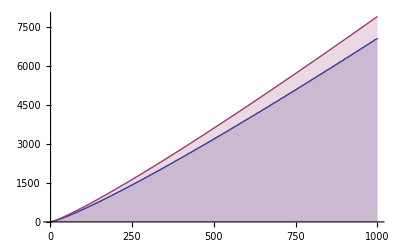

```mathematica
DiscretePlot[{ D1[n,2], LaguerreL[-2,Log[n]]}, {n,1,1000}]
```

```mathematica
Integrate[ 1/Log[x],{x,1.1,n},PrincipalValue->True]
```

ConditionalExpression[1.67577+LogIntegral[n],Im[n]≠0||Re[n]≥1.]

```mathematica
TestSum[ n_, z_, t_] := Sum[ N[Binomial[z,k] (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k])],{k,0, t}]
Grid[ Table[ { Re[TestSum[n, k,23]], N[LaguerreL[-k, Log[n]]]}, {n,10, 100, 10},{k,-5,5}]]
```

{0.966672,0.966672} | {0.727895,0.727895} | {0.0104133,0.0104133} | {-0.954221,-0.954221} | {-1.30259,-1.30259} | {1.,1.} | {10.,10.} | {33.0259,33.0259} | {82.5612,82.5612} | {178.953,178.953} | {354.26,354.26}
{0.853716,0.853716} | {1.37285,1.37285} | {0.993598,0.993598} | {-0.504259,-0.504259} | {-1.99573,-1.99573} | {1.,1.} | {20.,20.} | {79.9146,79.9146} | {229.573,229.573} | {558.593,558.593} | {1223.71,1223.71}
{0.345442,0.345447} | {1.4452,1.4452} | {1.59103,1.59103} | {-0.018323,-0.0183229} | {-2.4012,-2.4012} | {1.,1.} | {30.,30.} | {132.036,132.036} | {407.594,407.594} | {1053.4,1053.4} | {2433.46,2433.46}
{-0.182647,-0.182608} | {1.31842,1.31842} | {1.97883,1.97883} | {0.426157,0.426157} | {-2.68888,-2.68888} | {1.,1.} | {40.,40.} | {187.555,187.555} | {607.267,607.267} | {1633.79,1633.79} | {3910.39,3910.39}
{-0.66439,-0.664191} | {1.10954,1.10957} | {2.2416,2.2416} | {0.827916,0.827916} | {-2.91202,-2.91202} | {1.,1.} | {50.,50.} | {245.601,245.601} | {823.8,823.8} | {2283.51,2283.51} | {5611.57,5611.57}
{-1.09019,-1.08949} | {0.865209,0.86531} | {2.42308,2.42309} | {1.19314,1.19314} | {-3.09434,-3.09434} | {1.,1.} | {60.,60.} | {305.661,305.661} | {1054.23,1054.23} | {2992.07,2992.07} | {7508.1,7508.1}
{-1.46377,-1.46181} | {0.606799,0.607082} | {2.54836,2.5484} | {1.52786,1.52787} | {-3.2485,-3.2485} | {1.,1.} | {70.,70.} | {367.395,367.395} | {1296.53,1296.53} | {3752.05,3752.05} | {9578.84,9578.84}
{-1.79198,-1.78731} | {0.344902,0.345574} | {2.63302,2.6331} | {1.83702,1.83703} | {-3.38203,-3.38203} | {1.,1.} | {80.,80.} | {430.562,430.562} | {1549.21,1549.21} | {4557.87,4557.87} | {11807.5,11807.5}
{-2.08206,-2.0722} | {0.0849608,0.0863776} | {2.68727,2.68743} | {2.12451,2.12452} | {-3.49981,-3.49981} | {1.,1.} | {90.,90.} | {494.983,494.983} | {1811.14,1811.14} | {5405.17,5405.17} | {14181.2,14181.2}
{-2.34096,-2.32202} | {-0.170259,-0.167536} | {2.71814,2.71845} | {2.39343,2.39346} | {-3.60517,-3.60517} | {1.,1.} | {100.,100.} | {560.517,560.517} | {2081.41,2081.41} | {6290.43,6290.43} | {16689.3,16689.3}

```mathematica
Table[{N[Sum[(-1)^(k+1)/k ((-1)^k(1-Gamma[k,-Log[n]]/Gamma[k])),{k,1,30}]],N[ Limit[ (LaguerreL[-z,Log[n]]-1)/z,z->0]],N[LogIntegral[n]-Log[Log[n]]-EulerGamma]},{n,100,600,100}]//TableForm
```

28.0217-2.09386×10^-14 ⅈ | 28.0217 | 28.0217
47.9476-4.32162×10^-14 ⅈ | 47.9476 | 47.9476
66.0153-1.89547×10^-13 ⅈ | 66.0153 | 66.0153
83.0503-4.70318×10^-13 ⅈ | 83.0503 | 83.0503
99.3898-1.32718×10^-12 ⅈ | 99.3898 | 99.3898
115.213-2.10999×10^-12 ⅈ | 115.213 | 115.213

```mathematica
N[ Limit[ (LaguerreL[-z,Log[600]]-1)/z,z->0]]
```

115.213

```mathematica
N[LogIntegral[600]-Log[Log[600]]-EulerGamma]
```

115.213

```mathematica
Table[{N[Sum[(-1)^(k+1)/k ((-1)^k(1-Gamma[k,-Log[n]]/Gamma[k])),{k,1,30}]],N[Limit[(LaguerreL[-z,Log[n]]-1)/z,z->0]],N[LogIntegral[n]-Log[Log[n]]-EulerGamma]},{n,100,600,100}]//TableForm
```

28.0217-2.09386×10^-14 ⅈ | 28.0217 | 28.0217
47.9476-4.32162×10^-14 ⅈ | 47.9476 | 47.9476
66.0153-1.89547×10^-13 ⅈ | 66.0153 | 66.0153
83.0503-4.70318×10^-13 ⅈ | 83.0503 | 83.0503
99.3898-1.32718×10^-12 ⅈ | 99.3898 | 99.3898
115.213-2.10999×10^-12 ⅈ | 115.213 | 115.213

```mathematica
Limit[ Sum[ c^j/j,{j,2,Log[c,100]}],c->1]
```

Limit[-c-100 c LerchPhi[c,1,1+Log[100]/Log[c]]-Log[1-c],c→1]

```mathematica
Binomial[z,0]
```

1

```mathematica
Binomial[z,1]
```

z

```mathematica
Binomial[z,2]
```

1/2 (-1+z) z

```mathematica
Binomial[z,3]
```

1/6 (-2+z) (-1+z) z

```mathematica
Binomial[z,4]
```

1/24 (-3+z) (-2+z) (-1+z) z

```mathematica
Sum[ 1, {j,0,Floor[x-y]}]
```

1+Floor[x-y]

```mathematica
Sum[ 1, {j,0,Floor[x-y]}, {k,0, Floor[ x/(j+y)-y]}]
```

∑_(j=0)^Floor[x-y] ∑_(k=0)^Floor[-y+x/(j+y)] 1

```mathematica
Dd[x_,0,y_]:=1
Dd[x_,k_,y_]:=Sum[Dd[x/(j+y),k-1,y],{j,0,Floor[x-y]}]
Cc[x_,k_,y_]:=y^-k Dd[x y^k,k,y+1]
CSum[ x_, y_] := Sum[ (-1)^(k+1)/k Cc[ x, k, y],{k,1,10}]
```

```mathematica
Cd[x_, k_, y_] := (1/y)Sum[ Cd[ y x/(j+y+1), k-1, y], {j,0, Floor[y x - y-1]}]; Cd[ x_, 0, y_] := 1
Cz[x_, z_, k_, y_] := (z-k+1)/k(1/y)Sum[ Cz[ y x/(j+y+1), z, k-1, y], {j,0, Floor[y x - y-1]}]; Cz[ x_, z_, 0, y_] := 1
```

```mathematica
Cc[ 100, 2, 3]
```

995/3

```mathematica
Cd[ 100, 4,1]
```

184

```mathematica
Cz[ 100, 1,1,1]
```

99

```mathematica
pp[ x_, k_, y_] := (1/y)Sum[ 1/k - pp[ x y / ( j+y), k+1, y], {j, 1, Floor[ (x-1) y]}]
```

```mathematica
pp[100,1, 1]
```

428/15

```mathematica
D[pp[10,1,y],y]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

```mathematica
Expand[ (x y / ( j+y) -1 )y]
```

-y+(x y^2)/(j+y)

```mathematica
CSum[ 100, 13/10]
```

454930622410/17130345141

```mathematica
Expand[((x y) / (j+y) - 1 )y]
```

-y+(x y^2)/(j+y)

```mathematica
Limit[(1/y) Sum[ 1, {j,1,Floor[ x y - y]}],y->Infinity]
```

Limit[Floor[-y+x y]/y,y→∞]

```mathematica
D[ 1/y^2 Ccc, y]
```

```mathematica
Integrate[ -(2 Ccc)/y^3, {y, 11/10, 12/10}]
```

-(575 Ccc)/4356

```mathematica
1/((12/10)^2) - 1/((11/10)^2)
```

-575/4356

```mathematica
Integrate[ -(2 Ccc)/y^3, {y, bbb, Infinity}]
```

ConditionalExpression[-Ccc/bbb^2,Im[bbb]≠0||bbb>0]

```mathematica
Czz[x_, z_, k_, y_] := (z-k+1)/(y k)Sum[ 1+Czz[ x y/(j+y), z, k+1, y], {j,1, Floor[ x y - y]}]
```

```mathematica
1+Czz[ 100, -3, 1, 1]
```

47

```mathematica
d1[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
D1[n_,z_]:=Sum[d1[j,z],{j,1,n}]
```

```mathematica
D1[100,-3]
```

47

```mathematica
F[ n_, j_, k_, z_] := If[ n<j,0,(z-k+1)/k(1+F[ n/j, 2, k+1, z]) + F[ n, j+1, k, z]]
D1Alt[ n_, z_]  := 1 + F[ n, 2, 1, z ]
```

```mathematica
1+F[ 100, 2, 1, 3]
```

1471

```mathematica
d1[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
D1[n_,z_]:=Sum[d1[j,z],{j,1,n}]
F[n_,j_,k_,z_]:=If[n<j,0,(z-k+1)/k(1+F[n/j,2,k+1,z])+F[n,j+1,k,z]]
D1Alt[n_,z_]:=1+F[n,2,1,z]
Grid[Table[{D1[a=100,s+t I],D1Alt[a,s+t I]},{s,-1.3,4,.7},{t,-1.3,4,.7}]]
```

{10.4793+28.7121 ⅈ,10.4793+28.7121 ⅈ} | {5.72468+11.2587 ⅈ,5.72468+11.2587 ⅈ} | {6.03456-1.77709 ⅈ,6.03456-1.77709 ⅈ} | {5.94691-15.6189 ⅈ,5.94691-15.6189 ⅈ} | {15.2681-34.9044 ⅈ,15.2681-34.9044 ⅈ} | {58.5435-59.5846 ⅈ,58.5435-59.5846 ⅈ} | {173.704-80.8227 ⅈ,173.704-80.8227 ⅈ} | {409.891-76.8935 ⅈ,409.891-76.8935 ⅈ}
{-21.9794+33.2704 ⅈ,-21.9794+33.2704 ⅈ} | {-9.29577+6.6042 ⅈ,-9.29577+6.6042 ⅈ} | {-3.93641-0.702512 ⅈ,-3.93641-0.702512 ⅈ} | {-12.975-11.3196 ⅈ,-12.975-11.3196 ⅈ} | {-23.7041-47.2133 ⅈ,-23.7041-47.2133 ⅈ} | {-4.16474-124.722 ⅈ,-4.16474-124.722 ⅈ} | {95.5007-249.632 ⅈ,95.5007-249.632 ⅈ} | {340.872-412.252 ⅈ,340.872-412.252 ⅈ}
{-70.5899-1.50386 ⅈ,-70.5899-1.50386 ⅈ} | {-13.7213-18.1133 ⅈ,-13.7213-18.1133 ⅈ} | {3.81025+3.79964 ⅈ,3.81025+3.79964 ⅈ} | {-26.9749+19.1944 ⅈ,-26.9749+19.1944 ⅈ} | {-89.9388-16.1483 ⅈ,-89.9388-16.1483 ⅈ} | {-144.356-139.879 ⅈ,-144.356-139.879 ⅈ} | {-126.266-377.33 ⅈ,-126.266-377.33 ⅈ} | {49.351-735.771 ⅈ,49.351-735.771 ⅈ}
{-109.692-116.693 ⅈ,-109.692-116.693 ⅈ} | {25.3505-82.1743 ⅈ,25.3505-82.1743 ⅈ} | {64.0826+14.9568 ⅈ,64.0826+14.9568 ⅈ} | {-4.67506+101.541 ⅈ,-4.67506+101.541 ⅈ} | {-160.825+105.357 ⅈ,-160.825+105.357 ⅈ} | {-353.522-38.304 ⅈ,-353.522-38.304 ⅈ} | {-502.525-380.071 ⅈ,-502.525-380.071 ⅈ} | {-500.378-949.919 ⅈ,-500.378-949.919 ⅈ}
{-89.6457-364.055 ⅈ,-89.6457-364.055 ⅈ} | {165.919-209.786 ⅈ,165.919-209.786 ⅈ} | {237.081+36.8175 ⅈ,237.081+36.8175 ⅈ} | {110.164+267.906 ⅈ,110.164+267.906 ⅈ} | {-190.242+376.688 ⅈ,-190.242+376.687 ⅈ} | {-601.821+264.819 ⅈ,-601.821+264.819 ⅈ} | {-1025.88-150.194 ⅈ,-1025.88-150.194 ⅈ} | {-1329.51-927.604 ⅈ,-1329.51-927.604 ⅈ}
{69.3293-807.552 ⅈ,69.3293-807.552 ⅈ} | {497.243-430.789 ⅈ,497.243-430.789 ⅈ} | {614.555+74.3692 ⅈ,614.555+74.3692 ⅈ} | {404.806+557.989 ⅈ,404.806+557.989 ⅈ} | {-102.401+871.308 ⅈ,-102.401+871.308 ⅈ} | {-831.921+874.96 ⅈ,-831.921+874.96 ⅈ} | {-1664.43+447.187 ⅈ,-1664.43+447.187 ⅈ} | {-2438.58-507.936 ⅈ,-2438.58-507.936 ⅈ}
{484.136-1524.88 ⅈ,484.136-1524.88 ⅈ} | {1146.82-781.362 ⅈ,1146.82-781.362 ⅈ} | {1326.79+133.656 ⅈ,1326.79+133.656 ⅈ} | {1004.52+1019.94 ⅈ,1004.52+1019.94 ⅈ} | {215.141+1678.53 ⅈ,215.141+1678.53 ⅈ} | {-952.011+1920.83 ⅈ,-952.011+1920.83 ⅈ} | {-2354.8+1577.59 ⅈ,-2354.8+1577.59 ⅈ} | {-3800.46+508.005 ⅈ,-3800.46+508.005 ⅈ}
{1316.61-2608.99 ⅈ,1316.61-2608.99 ⅈ} | {2288.19-1304.73 ⅈ,2288.19-1304.73 ⅈ} | {2550.42+221.895 ⅈ,2550.42+221.895 ⅈ} | {2080.38+1711.29 ⅈ,2080.38+1711.29 ⅈ} | {919.284+2905.28 ⅈ,919.284+2905.28 ⅈ} | {-828.+3556.97 ⅈ,-828.+3556.97 ⅈ} | {-2994.35+3440.6 ⅈ,-2994.35+3440.6 ⅈ} | {-5352.56+2361.41 ⅈ,-5352.56+2361.41 ⅈ}

```mathematica
zz1[n_,k_]:=(-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k])
zz2[n_, k_] :=Integrate[(-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{t,-Log[n],0}]
zz2a[n_, k_] :=Integrate[ t^(k-1)E^(-t),{t,-Log[n],0}]
```

```mathematica
zz1[100,0.01]
```

1.30358+0.0820144 ⅈ

```mathematica
zz2[100,0.01]
```

1.30358+0.0820144 ⅈ

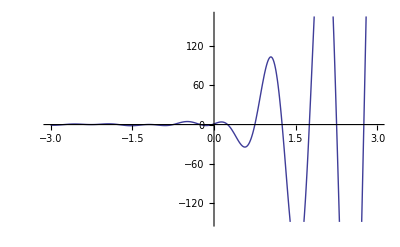

```mathematica
Plot[ Re[zz1[100,z]],{z,-3,3}]
```

```mathematica
Plot[ Re[zz2[100,z]],{z,-3,3}]
```

$Aborted

```mathematica
ff4a[ n_, z_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
ff4a[100,z]
```

-1+LaguerreL[-z,Log[100]]

```mathematica
TestSum[n_,z_,t_]:=Sum[N[Binomial[z,k] (-1)^k (1-Gamma[k,-Log[n]]/Gamma[k])],{k,0,t}]
Grid[Table[{Re[TestSum[n,k,23]],N[LaguerreL[-k,Log[n]]]},{n,10,100,10},{k,-5,5}]]
```

{0.966672,0.966672} | {0.727895,0.727895} | {0.0104133,0.0104133} | {-0.954221,-0.954221} | {-1.30259,-1.30259} | {1.,1.} | {10.,10.} | {33.0259,33.0259} | {82.5612,82.5612} | {178.953,178.953} | {354.26,354.26}
{0.853716,0.853716} | {1.37285,1.37285} | {0.993598,0.993598} | {-0.504259,-0.504259} | {-1.99573,-1.99573} | {1.,1.} | {20.,20.} | {79.9146,79.9146} | {229.573,229.573} | {558.593,558.593} | {1223.71,1223.71}
{0.345442,0.345447} | {1.4452,1.4452} | {1.59103,1.59103} | {-0.018323,-0.0183229} | {-2.4012,-2.4012} | {1.,1.} | {30.,30.} | {132.036,132.036} | {407.594,407.594} | {1053.4,1053.4} | {2433.46,2433.46}
{-0.182647,-0.182608} | {1.31842,1.31842} | {1.97883,1.97883} | {0.426157,0.426157} | {-2.68888,-2.68888} | {1.,1.} | {40.,40.} | {187.555,187.555} | {607.267,607.267} | {1633.79,1633.79} | {3910.39,3910.39}
{-0.66439,-0.664191} | {1.10954,1.10957} | {2.2416,2.2416} | {0.827916,0.827916} | {-2.91202,-2.91202} | {1.,1.} | {50.,50.} | {245.601,245.601} | {823.8,823.8} | {2283.51,2283.51} | {5611.57,5611.57}
{-1.09019,-1.08949} | {0.865209,0.86531} | {2.42308,2.42309} | {1.19314,1.19314} | {-3.09434,-3.09434} | {1.,1.} | {60.,60.} | {305.661,305.661} | {1054.23,1054.23} | {2992.07,2992.07} | {7508.1,7508.1}
{-1.46377,-1.46181} | {0.606799,0.607082} | {2.54836,2.5484} | {1.52786,1.52787} | {-3.2485,-3.2485} | {1.,1.} | {70.,70.} | {367.395,367.395} | {1296.53,1296.53} | {3752.05,3752.05} | {9578.84,9578.84}
{-1.79198,-1.78731} | {0.344902,0.345574} | {2.63302,2.6331} | {1.83702,1.83703} | {-3.38203,-3.38203} | {1.,1.} | {80.,80.} | {430.562,430.562} | {1549.21,1549.21} | {4557.87,4557.87} | {11807.5,11807.5}
{-2.08206,-2.0722} | {0.0849608,0.0863776} | {2.68727,2.68743} | {2.12451,2.12452} | {-3.49981,-3.49981} | {1.,1.} | {90.,90.} | {494.983,494.983} | {1811.14,1811.14} | {5405.17,5405.17} | {14181.2,14181.2}
{-2.34096,-2.32202} | {-0.170259,-0.167536} | {2.71814,2.71845} | {2.39343,2.39346} | {-3.60517,-3.60517} | {1.,1.} | {100.,100.} | {560.517,560.517} | {2081.41,2081.41} | {6290.43,6290.43} | {16689.3,16689.3}

```mathematica
TestSum[n_,z_,t_]:=Sum[N[Binomial[z,k] (-1)^k (1-Gamma[k,-Log[n]]/Gamma[k])],{k,0,t}]
```

```mathematica
TestSum[ 100, 2, 30]
```

560.517-4.41506×10^-14 ⅈ

```mathematica
zz1[n_,k_]:=(-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k])
zz2[n_, k_] :=Integrate[(-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{t,-Log[n],0}]
```

```mathematica
N[zz2[100,2]]
```

361.517

```mathematica
aff2[ n_, z_] := Sum[ Binomial[z,k] (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k]),{k,0, Infinity}]
```

```mathematica
aff2[100,2,40]
```

200-Gamma[2,-Log[100]]

```mathematica
Limit[ Sum[(j+1) c^j/j ,{j,1, Log[c,n]}],c->1]
```

Limit[(-c+c n+c n LerchPhi[c,1,1+Log[n]/Log[c]]-c^2 n LerchPhi[c,1,1+Log[n]/Log[c]]+Log[1-c]-c Log[1-c])/(-1+c),c→1]

```mathematica
Limit[ Sum[(j+1)(c-1)^2 c^j ,{j,1, Log[c,n]}],c->1]
```

1-n+n Log[n]

```mathematica
Limit[ Sum[(j+1)(j+2)(c-1)^3c^j ,{j,1, Log[c,n]}],c->1]
```

-2+2 n-2 n Log[n]+n Log[n]^2

```mathematica
N[Limit[ Sum[(j+1)(j+2)(j+3)(c-1)^4c^j ,{j,1, Log[c,n]}],c->1]/.n->100]
```

5573.28

```mathematica
Expand[LaguerreL[4, Log[n]]]
```

1-4 Log[n]+3 Log[n]^2-(2 Log[n]^3)/3+Log[n]^4/24

```mathematica
Gamma[ 4, -Log[100.]]
```

-5567.28+2.04539×10^-12 ⅈ

```mathematica
Limit[ Sum[j^z(c-1)^(z+1) c^j ,{j,1, Log[c,n]}],c->1]/.{z->4}
```

24 (-1+n)-24 n Log[n]+12 n Log[n]^2-4 n Log[n]^3+n Log[n]^4

```mathematica
N[Gamma[ 4, -Log[n]]/.n->100]
```

-5567.28+2.04539×10^-12 ⅈ

```mathematica
Limit[ Sum[ c^-j (c-1) ,{j,1, Log[c,n]}],c->1]
```

(-1+n)/n

```mathematica
Limit[ Sum[ c^j (c-1) ,{j,1, Log[c,n]}],c->1]
```

-1+n

```mathematica
Limit[ Sum[ c^j/j (c-1) ,{j,1, Log[c,n]}],c->1]
```

Limit[c n LerchPhi[c,1,1+Log[n]/Log[c]]-c^2 n LerchPhi[c,1,1+Log[n]/Log[c]]+Log[1-c]-c Log[1-c],c→1]

```mathematica
TestSum[n_,z_,t_]:=1+Sum[N[Binomial[z,k] (-1)^k (Gamma[k,0,-Log[n]]/Gamma[k])],{k,1,t}]
Grid[Table[Chop[Re[TestSum[n,k,80]]-N[LaguerreL[-k,Log[n]]]],{n,10,100,10},{k,-5,5}]]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.47048×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.51938×10^-10 | 2.2593×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
D1y1[ x_, s_, k_, y_ ]:= D1y1[x,s,k,y]=D1y1[ x, s,k-1, y] + y Sum[ (1+j y)^-s  D1y1[ x( 1+ j y)^-1, s,k-1, y],{j,1,(x-1)/y}]; D1y1[x_,s_,0,y_] := UnitStep[ x-1]
```

```mathematica
N[D1y1[ 10, -1,1,.0001]]
```

50.5004

```mathematica
LaguerreL[-3,Log[100.]]
```

2081.41

```mathematica
FullSimplify[(y(Zeta[s]-1)+1)^z-Sum[ Binomial[z,k] (y(Zeta[s]-1))^k,{k,0,Infinity}]]
```

0

```mathematica
(1/2) (1/2)^-s
```

2^(-1+s)

```mathematica
HurwitzZeta[2,2]
```

-1+π^2/6

```mathematica
{Limit[x^(s-1) HurwitzZeta[s,x+1],x->Infinity],1/(s-1)}
```

{1/(-1+s),1/(-1+s)}

```mathematica
Integrate[ y^-s, {y,1,x}]
```

ConditionalExpression[(x^-s (-x+x^s))/(-1+s),Re[x]≥0||x∉Reals]

```mathematica
Expand[(x^-s (-x+x^s))/(-1+s)]
```

```mathematica
1/(-1+s)-x^(1-s)/(-1+s)/.s->-3
```

-1/4+x^4/4

```mathematica
FullSimplify[x^-s (-x+x^s)]
```

1-x^(1-s)

```mathematica
Expand[(n^(1-s)-1)/(1-s)/.s->-4]
```

-1/5+n^5/5

```mathematica
Sum[ j^-s,{j,2,Floor[n]}]/.s->-4
```

-1-Floor[n]/30+Floor[n]^3/3+Floor[n]^4/2+Floor[n]^5/5

```mathematica
Integrate[ x^-s,{x,1,Infinity}]
```

ConditionalExpression[1/(-1+s),Re[s]>1]

```mathematica
1/(s-1) + Integrate[ D[ y^(1-s) Zeta[ s, y^-1+1],y],{y,0,1}]
```

1/(-1+s)+∫_0^1 ((1-s) y^-s Zeta[s,1+1/y]+s y^(-1-s) Zeta[1+s,1+1/y])ⅆy

```mathematica
Table[{Zeta[s]-1,1/(s-1)-Integrate[D[y^(s-1) Zeta[s,y+1],y],{y,1,Infinity}]},{s,2,6}]
```

{{-1+π^2/6,-1+π^2/6},{-1+Zeta[3],-1+Zeta[3]},{-1+π^4/90,-1+π^4/90},{-1+Zeta[5],-1+Zeta[5]},{-1+π^6/945,-1+π^6/945}}

```mathematica
f1[f_] := Integrate[ f[x],{x,1,Infinity}]
f2[f_] := Integrate[ f[1/x],{x,0,1}]
```

```mathematica
nn[x_] := 1/x^2
```

```mathematica
f1[nn]
```

1

```mathematica
f2[nn]
```

1/3

```mathematica
Integrate[Sin[x]/x,{x,1,Infinity}]
```

1/2 (π-2 SinIntegral[1])

```mathematica
Integrate[ Sin[1/r]/(1/r),{r,0,1}]
```

1/4 (-π+2 (Cos[1]+Sin[1]+SinIntegral[1]))

```mathematica
Dy[x_,y_,k_]:= Sum[y Dy[x (j y^-1+1)^-1,y,k-1],{j,1,(x-1)/y}];Dy[x_,y_,0]:=UnitStep[x-1]
```

```mathematica
Dy[100,2,1]
```

98

```mathematica
{Limit[(y^(s-1) HurwitzZeta[s,y+1])^k,y->Infinity],1/(s-1)^k}
```

{(1/(-1+s))^k,(-1+s)^-k}

```mathematica
Expand[(1-s)^2]
```

1-2 s+s^2

```mathematica
Expand[(s-1)^2]
```

1-2 s+s^2

```mathematica
Grid[Table[Chop[N[1/((s-1)^k)-Integrate[D[(Zeta[s,y+1]y^(s-1))^k,y],{y,1,Infinity}]]-N[(Zeta[s]-1)^k]],{s,2,4},{k,1,4}]]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
Log[Zeta[s,y+1]y^(s-1)+1]-FullSimplify[Sum[ (-1)^(k+1)/k(Zeta[s,y+1]y^(s-1))^k,{k,1,Infinity}]]
```

0

```mathematica
Limit[ Gamma[k,0,-Log[100]]/Gamma[k],k->0]
```

1

```mathematica
FullSimplify[Sum[ (1/k)( 2^((1-s)k) + (-1)^(k+1)((1-2^(1-s))Zeta[s])^k ),{k,1,Infinity}]]/.s->0
```

-ⅈ π+Log[3/2]

```mathematica
Log[Zeta[0]]
```

ⅈ π-Log[2]

```mathematica
Table[{Log[Zeta[s]],Limit[Sum[(x^(1-s))^j/j,{j,1,Infinity}]+Sum[(-1)^(k-1)/k((1-x^(1-s))Zeta[s]-1)^k,{k,1,Infinity}],x->2]},{s,0,0}]
```

{{ⅈ π-Log[2],-ⅈ π-Log[2]}}

```mathematica
{Log[Zeta[s]],Sum[(2^(1-s))^j/j,{j,1,Infinity}]+Sum[(-1)^(k-1)/k((1-2^(1-s))Zeta[s]-1)^k,{k,1,Infinity}]}/.s->0
```

{ⅈ π-Log[2],-ⅈ π-Log[2]}

```mathematica
ff5[ n_, z_, s_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^((s-1)t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
ff5[ n, z,s]/.{s->0}
```

ConditionalExpression[-1+LaguerreL[-z,Log[n]],-1≤Re[Log[n]]≤1||Log[n]∉Reals]

```mathematica
ff5[ n, z,s]/.{s->-1}
```

∫_(-Log[n])^0 ⅇ^(-2 t) z Hypergeometric1F1[1-z,2,t]ⅆt

```mathematica
ff5[ n, z,s]
```

∫_(-Log[n])^0 ⅇ^((-1+s) t) z Hypergeometric1F1[1-z,2,t]ⅆt

```mathematica
Limit[((-1+ff5[ n, z,s]/.s->2)/z),z->0]
```

$Aborted

```mathematica
N[-Gamma[0, -Log[100]]]
```

30.1261+3.14159 ⅈ

```mathematica
FullSimplify[Limit[Gamma[ 0, s Log[n]] - Gamma[ 0, (s-1)Log[n]]+Log[s/(s-1)],s->3]]/.n->100
```

1/2 (-2 ExpIntegralEi[-3 Log[100]]+2 ExpIntegralEi[-2 Log[100]]-Log[1/(3 Log[100])]+Log[3/(2 Log[100])]+Log[Log[100]]-Log[2 Log[100]])

```mathematica
Limit[ ff5[ n, z,s],z->0]
```

Limit[∫_(-Log[n])^0 ⅇ^((-1+s) t) z Hypergeometric1F1[1-z,2,t]ⅆt,z→0]

```mathematica
D[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^((s-1)t),{k,0, Infinity}],z]/.z->0
```

(ⅇ^((-1+s) t) (-1+ⅇ^t))/t

```mathematica
ff5[n,z,0]
```

ConditionalExpression[-1+LaguerreL[-z,Log[n]],-1≤Re[Log[n]]≤1||Log[n]∉Reals]

```mathematica
N[1/2 (-2 ExpIntegralEi[-3 Log[100]]+2 ExpIntegralEi[-2 Log[100]]-Log[1/(3 Log[100])]+Log[3/(2 Log[100])]+Log[Log[100]]-Log[2 Log[100]])]
```

0.405455

```mathematica
N[Gamma[0, s Log[100]]-Gamma[0,(s-1) Log[100]] + Log[ s/(s-1)]]/.s->-2
```

77381.+0. ⅈ

```mathematica
N[D[ff5[ 100, z,-2],z]/.z->0]
```

77381.

```mathematica
N[Gamma[0, 2 Log[10]]]
```

0.00182974

```mathematica
N[Gamma[0, Log[10]]]
```

0.0323898

```mathematica
N[Gamma[0, 2]]
```

0.0489005

```mathematica
NSum[ -1/k Gamma[k,0,-Log[100]]/Gamma[k],{k,1,Infinity}]
```

28.0217

```mathematica
-N[Gamma[0,-Log[100]]]
```

30.1261+3.14159 ⅈ

```mathematica
N[D[LaguerreL[ -z, Log[100]],z]/.z->0]
```

28.0217

```mathematica
N[LogIntegral[100]-Log[Log[100]]-EulerGamma]
```

28.0217

```mathematica
N[D[LaguerreL[ -z, Log[100]],{z,6}]/.z->0]
```

$Aborted

```mathematica
ff5[ n, z,s]
```

∫_(-Log[n])^0 ⅇ^((-1+s) t) z Hypergeometric1F1[1-z,2,t]ⅆt

```mathematica
Binomial[z,0]
```

1

```mathematica
Binomial[z,2]
```

1/2 (-1+z) z

```mathematica
Integrate[ y^-s, {y,1,n}]
```

ConditionalExpression[(n^-s (-n+n^s))/(-1+s),Re[n]≥0||n∉Reals]

```mathematica
Expand[(n^-s (-n+n^s))/(-1+s)]
```

1/(-1+s)-n^(1-s)/(-1+s)

```mathematica
Integrate[ (x y)^-s, {x,1,n},{y,1,n/x}]
```

ConditionalExpression[1/(-1+s)^2-(n^(1-s) (1+(-1+s) Log[n]))/(-1+s)^2,Re[n]≥0||n∉Reals]

```mathematica
Expand[1/(-1+s)^2-(n^(1-s) (1+(-1+s) Log[n]))/(-1+s)^2/.s->-1]
```

1/4-n^2/4+1/2 n^2 Log[n]

```mathematica
FullSimplify[1/(-1+s)^2-(n^(1-s) (1+(-1+s) Log[n]))/(-1+s)^2]
```

(n^-s (-n+n^s+(n-n s) Log[n]))/(-1+s)^2

```mathematica
∫_-Infinity^0 ⅇ^((-1+s) t) z Hypergeometric1F1[1-z,2,t]ⅆt
```

ConditionalExpression[-1+(s/(-1+s))^z,Re[s]>1]

```mathematica
ff2a[ n_, z_, t_,s_] := 1+Sum[ Binomial[z,k] (-1)^k ( GammaRegularized[ k, 0, (s-1)Log[n]](1-s)^-k),{k,1, t}]
```

```mathematica
ff2a[100,2,200,2]
```

149/50+GammaRegularized[2,0,Log[100]]

```mathematica
N[Sum[ Binomial[z,k] (-1)^k ( GammaRegularized[ k, 0, (s-1)Log[n]](1-s)^-k),{k,1, Infinity}]/.{n->10,s->2,z->3}]
```

5.11387

```mathematica
N[ff5[ 10,3,2]]
```

5.11387

```mathematica
E^{I Log[Zeta[s]]}
```

{Zeta[s]^ⅈ}

```mathematica
FI[n_]:=FI[n]=FactorInteger[n];FI[1]:={}
dzeta[j_,z_]:=dzeta[j,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[j]}]
zeta[n_,s_,z_]:=Sum[j^-s dzeta[j,z],{j,1,n}]
cosz[ n_, s_,t_] := Sum[ (-1)^k zeta[n,s,2 k]/((2 k)!),{k,0,t}]
coszp[ n_, s_,t_] := Sum[ (-1)^k/((2k)!) Sum[ (2 Pi )^(2k-j) zeta[n,s,j],{j,0,2k}],{k,0,t}]
coszp2[ n_, s_,t_] := Sum[ (-1)^k/((2k)!) Sum[ (2 Pi )^(2k-j) zet[n,s,j],{j,0,2k}],{k,0,t}]
```

```mathematica
N[cosz[10000,2,30]]
```

-0.0743883

```mathematica
N[zeta[100,s,0]-zeta[100,s,2]/2+zeta[100,s,4]/24-zeta[100,s,6]/720+zeta[100,s,8]/(8!)-zeta[100,s,10]/(10!)+zeta[100,s,12]/(12!)]/.s->2
```

-0.0685789

```mathematica
N[Cos[Zeta[2]]]
```

-0.0740698

```mathematica
N[coszp[1000,2,20]]
```

1.3782

```mathematica
Sum[ (2 Pi )^(2r-j) zzz[n,j],{j,0,2r}]/.r->2
```

16 π^4 zzz[n,0]+8 π^3 zzz[n,1]+4 π^2 zzz[n,2]+2 π zzz[n,3]+zzz[n,4]

```mathematica
coszp2[100,2,3]
```

zet[100,2,0]+1/2 (-4 π^2 zet[100,2,0]-2 π zet[100,2,1]-zet[100,2,2])+1/24 (16 π^4 zet[100,2,0]+8 π^3 zet[100,2,1]+4 π^2 zet[100,2,2]+2 π zet[100,2,3]+zet[100,2,4])+1/720 (-64 π^6 zet[100,2,0]-32 π^5 zet[100,2,1]-16 π^4 zet[100,2,2]-8 π^3 zet[100,2,3]-4 π^2 zet[100,2,4]-2 π zet[100,2,5]-zet[100,2,6])

```mathematica
-Limit[D[Gamma[0,s Log[n]]-Gamma[0,(s-1)Log[n]]+Log[s/(s-1)],s],s->0]
```

-1+n-Log[n]

```mathematica
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1) Sum[j^-s zeta[n/j,s,z,k+1],{j,2,n}]
```

```mathematica
Limit[D[N[Expand[D[Expand[zeta[100,s,z,1]],s]/.s->0]],z],z->0]
```

-94.0453

```mathematica
N[Expand[D[Expand[zeta[100,s,z,1]],s]/.s->0]]
```

-94.0453 z-169.15 z^2-81.6195 z^3-17.6846 z^4-1.19616 z^5-0.0438125 z^6

```mathematica
tt[n_,z_] :=N[Expand[D[Expand[zeta[n,s,z,1]],s]/.s->0]]
tt2[n_,z_] :=D[zeta[n,s,z,1],s]/.s->0
lzeros[n_]:=List@@NRoots[tt[n,z]-1==0,z][[All,2]]
lzeros2[n_]:=List@@NRoots[tt2[n,z]-1==0,z][[All,2]]
```

```mathematica
tt[100,z]
```

-94.0453 z-169.15 z^2-81.6195 z^3-17.6846 z^4-1.19616 z^5-0.0438125 z^6

```mathematica
lzeros[100]
```

{-10.6971-12.1993 ⅈ,-10.6971+12.1993 ⅈ,-2.54005-1.8272 ⅈ,-2.54005+1.8272 ⅈ,-0.816685,-0.0108436}

```mathematica
-Sum[ j^-1,{j,lzeros[100]}]
```

94.0453+0. ⅈ

```mathematica
-1+Product[ 1-1/j,{j,lzeros[1000]}]
```

$Aborted

```mathematica
Sum[N[Log[j]],{j,1,1000}]
```

363.739

```mathematica
lzeros2[100]
```

{-10.6971-12.1993 ⅈ,-10.6971+12.1993 ⅈ,-2.54005-1.8272 ⅈ,-2.54005+1.8272 ⅈ,-0.816685,-0.0108436}

```mathematica
-1+Product[ 1+1/j,{j,lzeros[100]}]
```

10.0174-8.88178×10^-16 ⅈ

```mathematica
tt[100,-1]
```

-10.0174

```mathematica
tt[100,2]
```

-1841.68

```mathematica
D[tt[100,z],z]/.z->0
```

-94.0453

```mathematica
D[tt[100,z],{z,2}]/.z->0
```

-338.3

```mathematica
-N[Sum[ Log[j]+Log[k],{j,1,100},{k,1,Floor[100/j]}]]
```

-1841.68

```mathematica
-N[Sum[ Log[j],{j,1,100},{k,1,Floor[100/j]}]]
```

-920.841

```mathematica
tt[100,2]-2tt[100,1]+tt[100,0]
```

-1114.2

```mathematica
d2[n_, s_, k_] := Sum[ j^-s d2[n/j, s,k-1],{j,2,n}]
d2[n_, s_, 0] := UnitStep[n-1]
```

```mathematica
N[D[Expand[d2[100,s,2]],s]/.s->0]
```

-1114.2

```mathematica
N[D[Sum[ (j k)^-s,{j,2,100},{k,2,100/j}],s]/.s->0]
```

-1114.2

```mathematica
N[Sum[ D[(j k)^-s,s]/.s->0,{j,2,100},{k,2,100/j}]]
```

-1114.2

```mathematica
Expand[D[(j k)^-s Kap[j] Kap[k],s]/.s->0]
```

-Kap[j] Kap[k] Log[j k]

```mathematica
2N[Sum[ -Log[j],{j,2,100},{k,2,100/j}]]
```

-1114.2

```mathematica
N[D[Sum[ (j k)^-s,{j,1,100},{k,1,100/j}],s]/.s->0]
```

-1841.68

```mathematica
tt[100,2]
```

-1841.68

```mathematica
N[Limit[D[Expand[Limit[D[zeta[100,s,z,1],z],z->0]],s],s->0]]
```

-94.0453

```mathematica
N[Limit[D[Expand[Limit[D[zeta[100,s,z,1],{z,2}],z->0]],s],s->0]]
```

-338.3

```mathematica
N[Limit[D[Expand[Limit[D[zeta[100,s,z,1],{z,3}],z->0]],s],s->0]]
```

-489.717

```mathematica
K[n_] := K[n] = FullSimplify[MangoldtLambda[n]/Log[n]]
K[1] := 0
-2N[Sum[ K[j]K[k]Log[k],{j,2,100},{k,2,100/j}]]
-3N[Sum[ K[j]K[k]K[l]Log[l],{j,2,100},{k,2,100/j}, {l,2,100/(j k)}]]
```

-338.3

-489.717

```mathematica
3/2 N[ Sum[ K[j] N[Limit[D[Expand[Limit[D[zeta[Floor[100/j],s,z,1],{z,2}],z->0]],s],s->0]],{j,2,100}]]
```

-489.717

```mathematica
D[(j+y)^-s,s]/.s->0
```

-Log[j+y]

```mathematica
D[ (1+j / y)^-s, s]/.s->0
```

-Log[1+j/y]

```mathematica
D[ ((1+j / y)(1+k/y))^-s, s]/.s->0
```

-Log[(1+j/y) (1+k/y)]

```mathematica
Sum[ (-1)^(k+1)/k x^k,{k,1,Infinity}]
```

Log[1+x]

```mathematica
tt[n_,z_] :=N[Expand[D[Expand[zeta[n,s,z,1]],s]/.s->0]]
tt2[n_,z_] :=D[zeta[n,s,z,1],s]/.s->0
lzeros[n_]:=List@@NRoots[tt[n,z]-1==0,z][[All,2]]
lzeros2[n_]:=List@@NRoots[tt2[n,z]-1==0,z][[All,2]]
pr[n_] := E^(Product[ 1-1/j,{j,lzeros[n]}])/E
```

```mathematica
pr[5]
```

120.

```mathematica
FullSimplify[ E^((1-1/a) (1-1/b) (1-1/c)(1-1/ d) )/E]
```

$Aborted

```mathematica
E^(3+1)
```

ⅇ^4

```mathematica
E^3 E
```

ⅇ^4

```mathematica
E^(a b)
```

ⅇ^(a b)

```mathematica
lzeros[5]
```

{-5.65162,-0.255271}

```mathematica
E^((1-1/-5.6516195112740135)(1-1/-0.2552710843345051))/E
```

120.

```mathematica
Table[lzeros2[n],{n,3,40}]//TableForm
```

Part::partd: Part specification (z == -0.558111) ⟦ All, 2 ⟧ is longer than depth of object.

z==-0.558111 | All | 2 |  | 
-3.12301 | -0.461957 |  |  | 
-5.65162 | -0.255271 |  |  | 
-1.34947 | -0.298212 |  |  | 
-2.25209 | -0.178692 |  |  | 
-7.6933 | -2.31459 | -0.162038 |  | 
-11.3756 | -1.82531 | -0.138961 |  | 
-18.7891 | -1.04804 | -0.146528 |  | 
-18.3869 | -1.4916 | -0.105207 |  | 
-3.17547 | -1.85831 | -0.106645 |  | 
-2.529-1.11322 ⅈ | -2.529+1.11322 ⅈ | -0.082424 |  | 
-5.30607 | -1.41111 | -0.0840496 |  | 
-7.43365 | -0.985929 | -0.0858659 |  | 
-9.34366-4.54503 ⅈ | -9.34366+4.54503 ⅈ | -0.986275 | -0.0812942 | 
-9.19869-4.27982 ⅈ | -9.19869+4.27982 ⅈ | -1.29244 | -0.0650671 | 
-27.3088 | -3.51173 | -1.3787 | -0.0654685 | 
-27.35 | -2.7197 | -2.14057 | -0.0543648 | 
-41.641 | -1.76741-0.826514 ⅈ | -1.76741+0.826514 ⅈ | -0.0546057 | 
-40.9372 | -2.92864 | -1.30944 | -0.0551387 | 
-40.194 | -4.01863 | -0.962081 | -0.0557025 | 
-40.2132 | -3.74722 | -1.2231 | -0.0469664 | 
-4.64026-2.26986 ⅈ | -4.64026+2.26986 ⅈ | -1.23385 | -0.0470746 | 
-4.65745-2.78721 ⅈ | -4.65745+2.78721 ⅈ | -1.20282 | -0.0437387 | 
-4.77647-3.69903 ⅈ | -4.77647+3.69903 ⅈ | -0.964492 | -0.0440295 | 
-5.2026-3.33709 ⅈ | -5.2026+3.33709 ⅈ | -0.965617 | -0.0420146 | 
-8.48722 | -4.50353 | -0.962248 | -0.0421406 | 
-8.65164 | -4.12121 | -1.18562 | -0.0366638 | 
-16.2813 | -1.47436-0.650513 ⅈ | -1.47436+0.650513 ⅈ | -0.0366574 | 
-16.3055 | -1.46438-0.88773 ⅈ | -1.46438+0.88773 ⅈ | -0.0324145 | 
-14.6954-12.6407 ⅈ | -14.6954+12.6407 ⅈ | -1.45868-0.881441 ⅈ | -1.45868+0.881441 ⅈ | -0.0317248
-14.4871-12.4473 ⅈ | -14.4871+12.4473 ⅈ | -1.66687-0.449788 ⅈ | -1.66687+0.449788 ⅈ | -0.0318413
-14.262-12.2467 ⅈ | -14.262+12.2467 ⅈ | -2.60863 | -1.1752 | -0.0319605
-14.0171-12.0388 ⅈ | -14.0171+12.0388 ⅈ | -3.32189 | -0.951594 | -0.0320825
-54.1561 | -4.10982-2.0086 ⅈ | -4.10982+2.0086 ⅈ | -0.951498 | -0.0321116
-54.1552 | -4.01762-1.85249 ⅈ | -4.01762+1.85249 ⅈ | -1.1403 | -0.0286462
-54.2062 | -4.08339-2.55695 ⅈ | -4.08339+2.55695 ⅈ | -0.95764 | -0.0287356
-54.2574 | -4.11807-3.08061 ⅈ | -4.11807+3.08061 ⅈ | -0.837002 | -0.0288268
-77.312 | -3.23628-2.85347 ⅈ | -3.23628+2.85347 ⅈ | -0.833711 | -0.0288563

```mathematica
Expand[(1-1/r)^4]
```

1+1/r^4-4/r^3+6/r^2-4/r

```mathematica
Log[1-1/r]
```

Log[1-1/r]

```mathematica
-Sum[ r^-k k^-1,{k,1,Infinity}]
```

Log[(-1+r)/r]

```mathematica
E^(a+b)
```

ⅇ^(a+b)

```mathematica
E^a E^b
```

ⅇ^(a+b)

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
pp[n_, s_, 0] := UnitStep[n-1]
pp[n_, s_, k_] := pp[n,s,k]=Sum[ (-1)^(j+1) 1/(2j - 1) (2 j -1)^-s pp[Floor[n/(2 j - 1)],s, k-1],{j,2,n}]
pz[n_, s_, z_] := Sum[ bin[ z,k] pp[n,s,k],{k,0,Log[2,n]}]
pzeros[n_, s_]:=List@@NRoots[pz[n,s,z]==0,z][[All,2]]
```

```mathematica
N[pz[1141,N[ZetaZero[1]],1]]
```

1.20656+0.182392 ⅈ

```mathematica
N[Expand[pz[400,z]]]
```

1.-0.239591 z+0.0250854 z^2-0.000295886 z^3-0.00101557 z^4-0.0000342936 z^5

```mathematica
Table[pzeros[n,N[ZetaZero[1]]],{n,420,440}]
```

{{-16.6813+12.2121 ⅈ,-9.25821-12.8105 ⅈ,-9.01788-1.39455 ⅈ,-4.33498+6.68041 ⅈ,5.37644+8.45781 ⅈ},{-16.684+12.2159 ⅈ,-9.25778-12.8078 ⅈ,-9.02221-1.40204 ⅈ,-4.32628+6.67959 ⅈ,5.37429+8.45957 ⅈ},{-16.684+12.2159 ⅈ,-9.25778-12.8078 ⅈ,-9.02221-1.40204 ⅈ,-4.32628+6.67959 ⅈ,5.37429+8.45957 ⅈ},{-17.3587+11.5569 ⅈ,-8.9324-12.7647 ⅈ,-8.91464-1.10664 ⅈ,-4.14445+6.86345 ⅈ,5.43429+8.5963 ⅈ},{-17.3587+11.5569 ⅈ,-8.9324-12.7647 ⅈ,-8.91464-1.10664 ⅈ,-4.14445+6.86345 ⅈ,5.43429+8.5963 ⅈ},{-16.644+12.1671 ⅈ,-9.25798-12.7852 ⅈ,-9.04194-1.3936 ⅈ,-4.3379+6.69241 ⅈ,5.36587+8.46456 ⅈ},{-16.644+12.1671 ⅈ,-9.25798-12.7852 ⅈ,-9.04194-1.3936 ⅈ,-4.3379+6.69241 ⅈ,5.36587+8.46456 ⅈ},{-16.6245+12.2589 ⅈ,-9.28234-12.7486 ⅈ,-9.08343-1.4599 ⅈ,-4.31857+6.62727 ⅈ,5.39294+8.46768 ⅈ},{-16.6245+12.2589 ⅈ,-9.28234-12.7486 ⅈ,-9.08343-1.4599 ⅈ,-4.31857+6.62727 ⅈ,5.39294+8.46768 ⅈ},{-15.2804+13.5795 ⅈ,-10.0185-12.6962 ⅈ,-9.28282-2.17251 ⅈ,-4.6047+6.19788 ⅈ,5.27045+8.2366 ⅈ},{-15.2804+13.5795 ⅈ,-10.0185-12.6962 ⅈ,-9.28282-2.17251 ⅈ,-4.6047+6.19788 ⅈ,5.27045+8.2366 ⅈ},{-15.2776+13.5762 ⅈ,-10.0194-12.6991 ⅈ,-9.27799-2.16574 ⅈ,-4.61289+6.19942 ⅈ,5.27197+8.23447 ⅈ},{-15.2776+13.5762 ⅈ,-10.0194-12.6991 ⅈ,-9.27799-2.16574 ⅈ,-4.61289+6.19942 ⅈ,5.27197+8.23447 ⅈ},{-15.2802+13.5797 ⅈ,-10.0183-12.6963 ⅈ,-9.28322-2.17213 ⅈ,-4.60488+6.19737 ⅈ,5.2706+8.23668 ⅈ},{-15.2802+13.5797 ⅈ,-10.0183-12.6963 ⅈ,-9.28322-2.17213 ⅈ,-4.60488+6.19737 ⅈ,5.2706+8.23668 ⅈ},{-16.7897+12.585 ⅈ,-9.32167-12.8773 ⅈ,-8.97514-1.54043 ⅈ,-4.26161+6.54524 ⅈ,5.43217+8.43278 ⅈ},{-16.7897+12.585 ⅈ,-9.32167-12.8773 ⅈ,-8.97514-1.54043 ⅈ,-4.26161+6.54524 ⅈ,5.43217+8.43278 ⅈ},{-16.8321+12.5109 ⅈ,-9.30991-12.9175 ⅈ,-8.92084-1.49385 ⅈ,-4.25993+6.60726 ⅈ,5.40685+8.43841 ⅈ},{-16.8321+12.5109 ⅈ,-9.30991-12.9175 ⅈ,-8.92084-1.49385 ⅈ,-4.25993+6.60726 ⅈ,5.40685+8.43841 ⅈ},{-16.8319+12.5069 ⅈ,-9.31163-12.9194 ⅈ,-8.91387-1.49033 ⅈ,-4.2661+6.6122 ⅈ,5.40759+8.43593 ⅈ},{-16.8319+12.5069 ⅈ,-9.31163-12.9194 ⅈ,-8.91387-1.49033 ⅈ,-4.2661+6.6122 ⅈ,5.40759+8.43593 ⅈ}}

```mathematica
4/N[pz[2500,-1]]
```

3.14866